```mathematica
a=5;
```

```mathematica
f[r_]:= 1/(r)^2(**UnitTriangle[r-a]*)
```

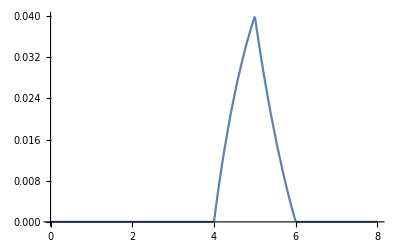

```mathematica
Plot[{f[r](*,UnitTriangle[r]*)},{r,0,a+3}]
```

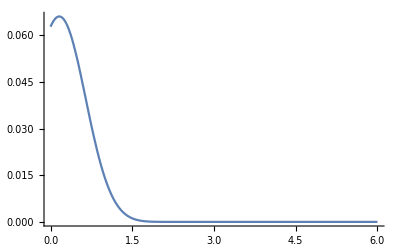

```mathematica
x[r_] :=Tanh[(π/2)Sinh[r]](*+(a-1)*)
w[t_]:=x'[t]
g[r_]:=f[x[r]]*x'[r]
g[r];
Plot[{(*x[r],w[r],*)g[r]},{r,0,a+1}, PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
NIntegrate[g[r],{r,0,a},Method->"Trapezoidal"]
```

0.05